# Jugando con las muestras del Gran Test 3

```mathematica
Get["/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/codigo/CoolTools.m"]
Get["/media/storage/ciencia/trabajo-con-carlos/tesis/tesis-erick/codigos/usefulFunctions.wl"]
```

```mathematica
SetDirectory["/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/gran_test_3"]
```

/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/gran_test_3

```mathematica
SetDirectory["/media/storage/ciencia/trabajo-con-carlos/tesis/"]
```

/media/storage/ciencia/trabajo-con-carlos/tesis

```mathematica
(*Función para importar una muestra y obtener su error máximo:*)
importAndGetMeanStd[sampleNum_, targetNum_, swapP_]:= With[{distsample = distsToTarget[Get["sampleMH_"<>ToString[sampleNum]<>".m"][[2]][[5001;;8000]], targets[[targetNum]], swapP]},
													 {Mean[distsample], StandardDeviation[distsample]}];
```

```mathematica
(*función para obtener las posiciones de todas las tuplas de parámetros donde estén involucrados
el target con la swapP indicados en sus argumentos:*)
getParamsPositions[target_, swapP_]:= With[{targetstate=(IdentityMatrix[2]+target PauliMatrix[3])/2},
									  Position[allParams,{_,_,swapP,targetstate},1]]
```

## Jugando con las muestras obtenidas para r_z = 0

### p = 0.3

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0 y p = 0.3 que se hayan generado:*)
sampleNumsRceroPptoTres = Select[Flatten@getParamsPositions[0, 0.3], ((# < 1153) || (1188 < # < 1283))&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRceroPptoTres = Map[#[[1;;2]]&, allParams[[sampleNumsRceroPptoTres]]];
```

```mathematica
(* Sólo los errores (i.e., promedio) de cada muestra con sus respectivas desviaciones. 
Tiene la siguiente estructura: {{prom1, StdDev1}, {prom2, StdDev2}, ...}*)
errorsRceroPptoTres = Map[importAndGetMeanStd[#, 1, 0.3]&, sampleNumsRceroPptoTres];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ, es decir, puntos tridimensionales (serían en 4D pues se incluyen las desviaciones):*)
errDataRceroPptoTres4D = MapThread[Append[#1, #2]&, {βδValuesRceroPptoTres, errorsRceroPptoTres}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRceroPptoTres2D = Map[(#[[{1,3}]]&) /@ errDataRceroPptoTres4D[[Flatten[Position[errDataRceroPptoTres4D, {_, #, _}]]]]&, deltas];
errDataRceroPptoTres2D = Map[{#[[1]], Apply[Around,#[[2]]]}&, #]& /@ errDataRceroPptoTres2D;
```

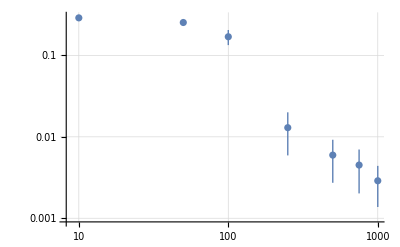
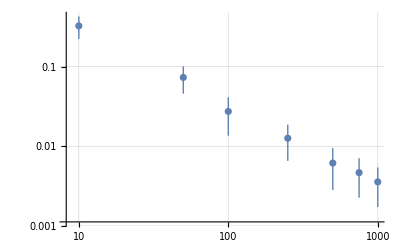
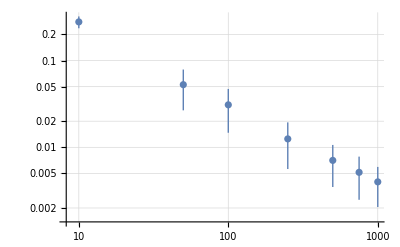
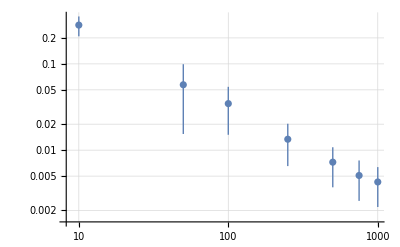
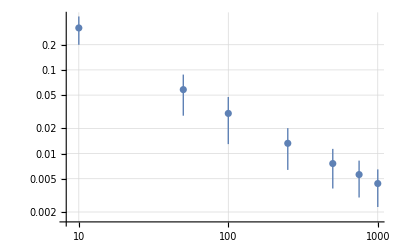
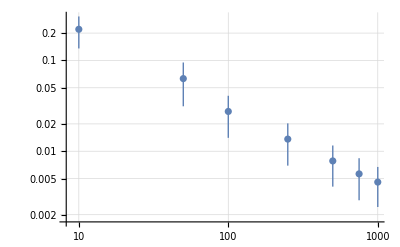
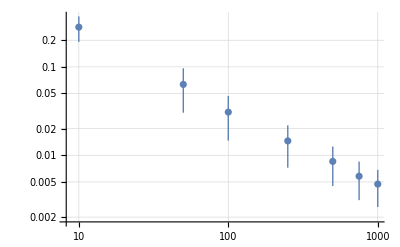
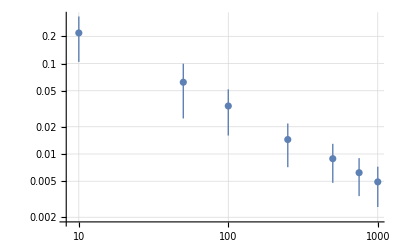

```mathematica
(*Graficamos una por una (por cada valor de δ):*)
Map[ListLogLogPlot[errDataRceroPptoTres2D[[#]], PlotLegends->deltas[[#]], GridLines->Automatic]&, Table[i, {i,22}]]
```

```mathematica
(*Todas juntas:*)
errDataRceroPptoTres2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRceroPptoTres2D;
```

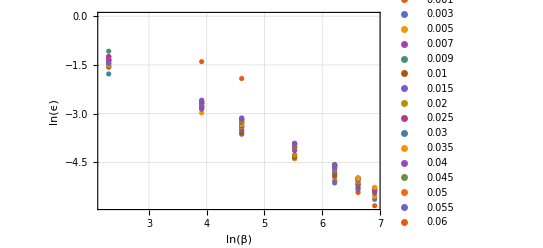
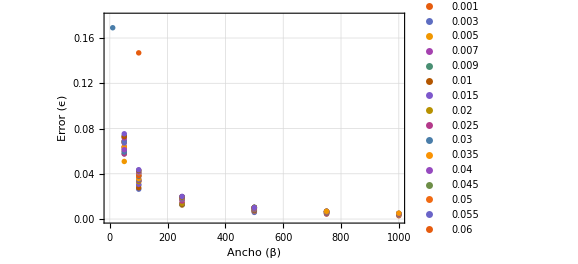
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[Log[errDataRceroPptoTres2D], PlotLegends->deltas, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{" ln(β)", "ln(ϵ)"}],
	   ListPlot[errDataRceroPptoTres2D, PlotLegends->deltas, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Ancho (β)", "Error (ϵ)"}]}}]
```

#### Regresión lineal

```mathematica
(*Regresión de los datos logarítmicos, con todas las deltas juntas*)
lmR0Pp3 = LinearModelFit[Flatten[Log[errDataRceroPptoTres2D],1], x, x]
```

FittedModel[0.676218-0.870149 x]

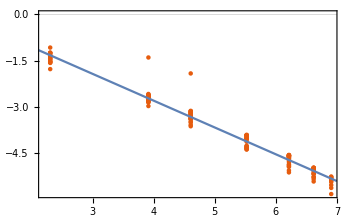
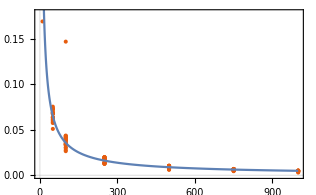
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 238.631 | 238.631 | 4631.94 | 1.70801×10^-107
Error | 137 | 7.05804 | 0.0515185 |  | 
Total | 138 | 245.689 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRceroPptoTres2D],1], PlotTheme->"Scientific"], Plot[lmR0Pp3[x],{x,0,7}]], lmR0Pp3["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRceroPptoTres2D,1], PlotTheme->"Scientific"], Plot[Exp[67/100]/x^(87/100), {x, 0,1000}, PlotRange->Full]]}
}]
```

### p = 0.5

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0 y p = 0.5 que se hayan generado:*)
sampleNumsRceroPptoCinco = Select[Flatten@getParamsPositions[0, 0.5], ((# < 1153) || (1188 < # < 1283))&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRceroPptoCinco = Map[#[[1;;2]]&, allParams[[sampleNumsRceroPptoCinco]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRceroPptoCinco = Map[importAndGetMeanStd[#, 1, 0.5]&, sampleNumsRceroPptoCinco];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRceroPptoCinco4D = MapThread[Append[#1, #2]&, {βδValuesRceroPptoCinco, errorsRceroPptoCinco}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRceroPptoCinco2D = Map[(#[[{1,3}]]&) /@ errDataRceroPptoCinco4D[[Flatten[Position[errDataRceroPptoCinco4D, {_, #, _}]]]]&, deltas];
errDataRceroPptoCinco2D = Map[{#[[1]], Apply[Around,#[[2]]]}&, #]& /@ errDataRceroPptoCinco2D;
```

```mathematica
(*Graficamos una por una (por cada valor de δ):*)
Map[ListLogLogPlot[errDataRceroPptoCinco2D[[#]], PlotLegends->deltas[[#]], GridLines->Automatic]&, Table[i, {i,22}]]
```

```mathematica
(*Todas juntas:*)
errDataRceroPptoCinco2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRceroPptoCinco2D;
```

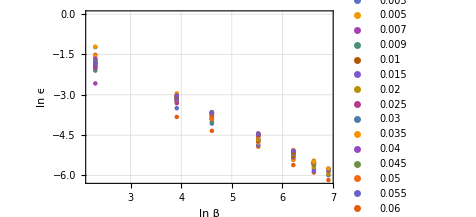
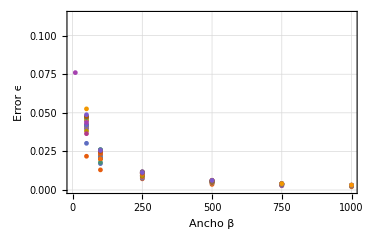
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[Log[errDataRceroPptoCinco2D], PlotLegends->deltas, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"ln β", "ln ϵ"}],
	   ListPlot[errDataRceroPptoCinco2D, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Ancho β", "Error ϵ"}]}
}]
```

#### Regresión lineal

```mathematica
lmR0Pp5 = LinearModelFit[Flatten[Log[errDataRceroPptoCinco2D],1], x, x]
```

FittedModel[0.262353-0.88187 x]

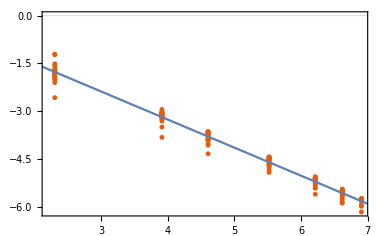
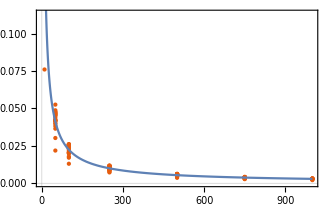
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 245.103 | 245.103 | 7829.59 | 9.21927×10^-123
Error | 137 | 4.28874 | 0.0313047 |  | 
Total | 138 | 249.392 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRceroPptoCinco2D],1], PlotTheme->"Scientific"], Plot[lmR0Pp5[x],{x,0,7}]], lmR0Pp5["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRceroPptoCinco2D,1], PlotTheme->"Scientific"], Plot[Exp[0.2623]/x^(0.8819), {x, 0,1000}, PlotRange->Full]]}
}]
```

### p = 0.8

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0 y p = 0.8 que se hayan generado:*)
sampleNumsRceroPptoOcho = Select[Flatten@getParamsPositions[0, 0.8], ((# < 1153) || (1188 < # < 1283)) && (# != 988)&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRceroPptoOcho = Map[#[[1;;2]]&, allParams[[sampleNumsRceroPptoOcho]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRceroPptoOcho = Map[importAndGetMeanStd[#, 1, 0.8]&, sampleNumsRceroPptoOcho];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRceroPptoOcho4D = MapThread[Append[#1, #2]&, {βδValuesRceroPptoOcho, errorsRceroPptoOcho}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRceroPptoOcho2D = Map[(#[[{1,3}]]&) /@ errDataRceroPptoOcho4D[[Flatten[Position[errDataRceroPptoOcho4D, {_, #, _}]]]]&, deltas];
errDataRceroPptoOcho2D = Map[{#[[1]], Apply[Around,#[[2]]]}&, #]& /@ errDataRceroPptoOcho2D;
```

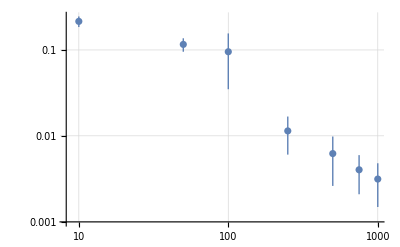
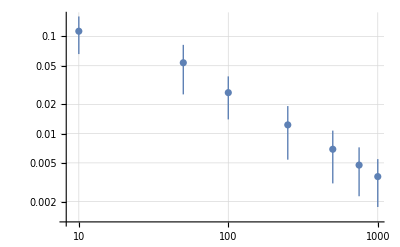
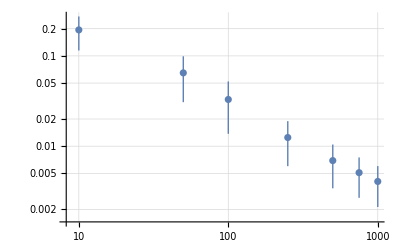
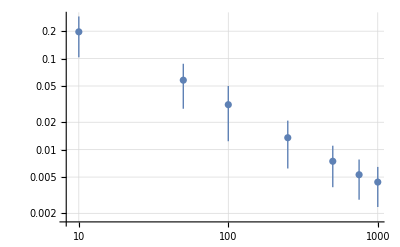
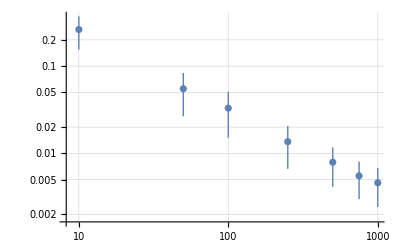
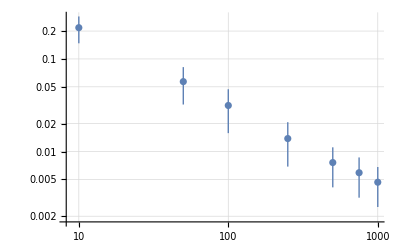
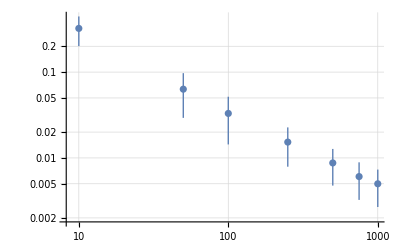
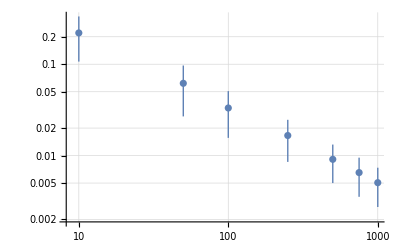

```mathematica
(*Graficamos una por una (por cada valor de δ):*)
Map[ListLogLogPlot[errDataRceroPptoOcho2D[[#]], PlotLegends->deltas[[#]], GridLines->Automatic]&, Table[i, {i,22}]]
```

```mathematica
(*Todas juntas:*)
errDataRceroPptoOcho2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRceroPptoOcho2D;
```

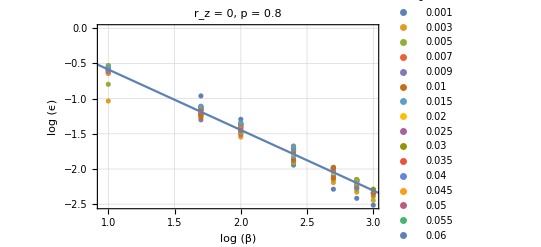

```mathematica
Show[ListPlot[Log10[errDataRceroPptoOcho2D], PlotTheme->"Detailed", GridLines->Automatic, FrameLabel->{"log (β)", "log (ϵ)"}, 
		PlotLegends->PointLegend[deltas, LegendLabel->"δ", LegendFunction->(Framed[#, RoundingRadius->5, FrameStyle->Black]&), LabelStyle->Black],
		FrameStyle->Black,
		PlotLabel->Style["r_z = 0, p = 0.8", Black]], 
	 Plot[0.274 - 0.86 x,{x,0,7}]]
```

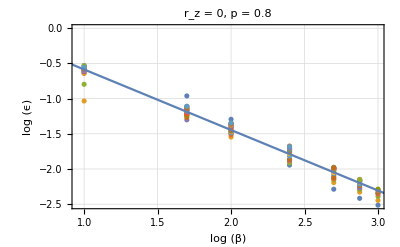

```mathematica
Show[ListPlot[Log10[errDataRceroPptoOcho2D], PlotTheme->"Detailed", FrameLabel->{"log (β)", "log (ϵ)"},
		FrameStyle->Black,
		PlotLabel->Style["r_z = 0, p = 0.8", Black]], 
	 Plot[0.274 - 0.86 x,{x,0,7}]]
```

```mathematica
Export["beta_vs_error.pdf", %48]
```

beta_vs_error.pdf

#### Regresión lineal

```mathematica
lmR0Pp8 = LinearModelFit[Flatten[Log10[errDataRceroPptoOcho2D],1], x, x]
```

FittedModel[0.273658-0.860747 x]

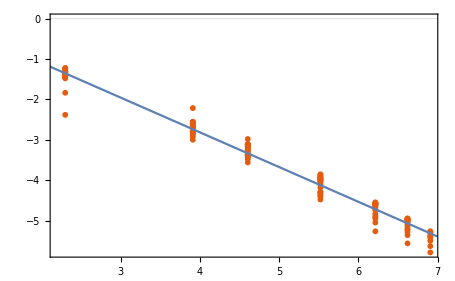
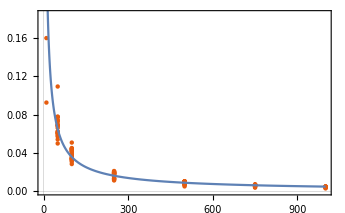
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 229.536 | 229.536 | 6171.6 | 1.41881×10^-114
Error | 135 | 5.02096 | 0.0371923 |  | 
Total | 136 | 234.557 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRceroPptoOcho2D],1], PlotTheme->"Scientific"], Plot[lmR0Pp8[x],{x,0,7}]], lmR0Pp8["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRceroPptoOcho2D,1], PlotTheme->"Scientific"], Plot[Exp[0.63]/x^(0.86), {x, 0,1000}, PlotRange->Full]]}
}]
```

## Jugando con las muestras obtenidas para r_z = 0.5

### p = 0.3

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.5 y p = 0.3 que se hayan generado:*)
sampleNumsRptoCincoPptoTres = Select[Flatten@getParamsPositions[0.5, 0.3], (# < 1153) || (1188 < # < 1283)&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoCincoPptoTres = Map[#[[1;;2]]&, allParams[[sampleNumsRptoCincoPptoTres]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoCincoPptoTres = Map[importAndGetMeanStd[#, 2, 0.3]&, sampleNumsRptoCincoPptoTres];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoCincoPptoTres4D = MapThread[Append[#1, #2]&, {βδValuesRptoCincoPptoTres, errorsRptoCincoPptoTres}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRptoCincoPptoTres2D = Map[(#[[{1,3}]]&) /@ errDataRptoCincoPptoTres4D[[Flatten[Position[errDataRptoCincoPptoTres4D, {_, #, _}]]]]&, deltas];
errDataRptoCincoPptoTres2D = Map[{#[[1]], Apply[Around,#[[2]]]}&, #]& /@ errDataRptoCincoPptoTres2D;
```

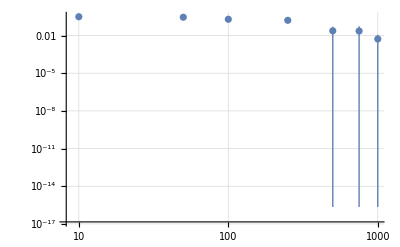
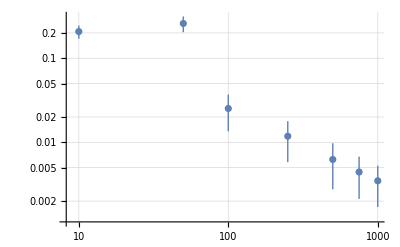
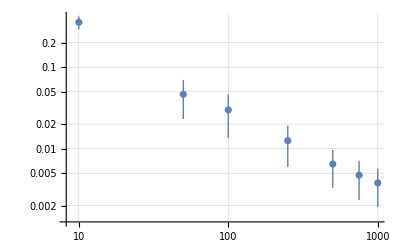
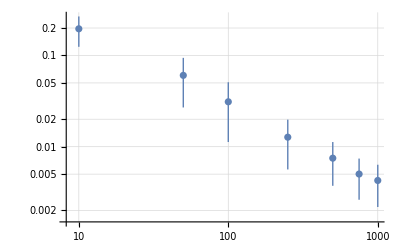
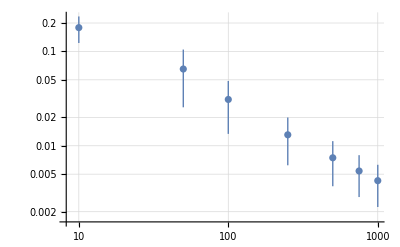
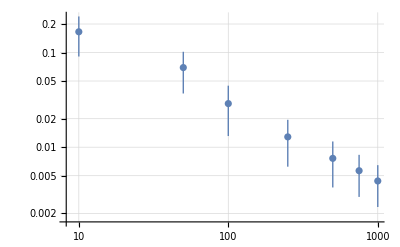
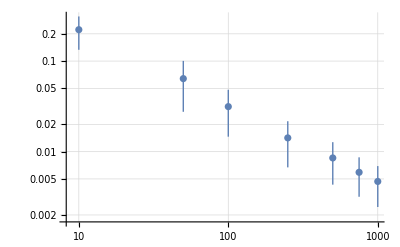
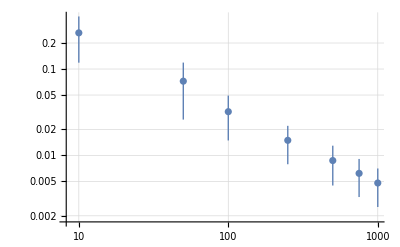

```mathematica
(*Graficamos una por una (por cada valor de δ):*)
Map[ListLogLogPlot[errDataRptoCincoPptoTres2D[[#]], PlotLegends->deltas[[#]], GridLines->Automatic]&, Table[i, {i,22}]]
```

```mathematica
(*Todas juntas:*)
errDataRptoCincoPptoTres2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoCincoPptoTres2D;
```

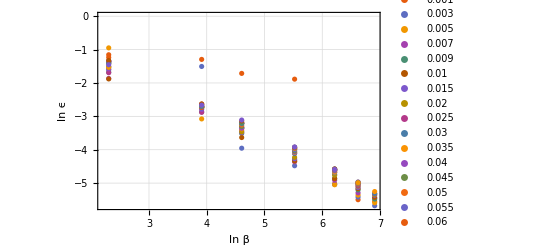
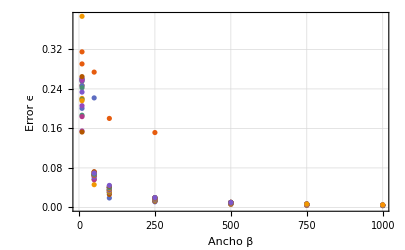
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[Log[errDataRptoCincoPptoTres2D], PlotLegends->deltas, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"ln β", "ln ϵ"}],
       ListPlot[errDataRptoCincoPptoTres2D, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Ancho β", "Error ϵ"}]}

}]
```

#### Regresión lineal

```mathematica
lmRp5Pp3 = LinearModelFit[Flatten[Log[errDataRptoCincoPptoTres2D],1], x, x]
```

FittedModel[0.646099-0.861268 x]

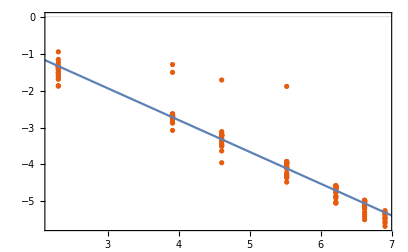
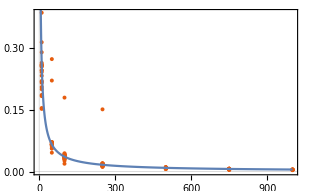
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 233.785 | 233.785 | 2083.17 | 9.64462×10^-85
Error | 137 | 15.3749 | 0.112225 |  | 
Total | 138 | 249.16 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoCincoPptoTres2D],1], PlotTheme->"Scientific"], Plot[lmRp5Pp3[x],{x,0,7}]], lmRp5Pp3["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoCincoPptoTres2D,1], PlotTheme->"Scientific"], Plot[Exp[0.646]/x^(0.86), {x, 0,1000}, PlotRange->Full]]}
}]
```

### p = 0.5

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.5 y p = 0.5 que se hayan generado:*)
sampleNumsRptoCincoPptoCinco = Select[Flatten@getParamsPositions[0.5, 0.5], (# < 1153) || (1188 < # < 1283)&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoCincoPptoCinco = Map[#[[1;;2]]&, allParams[[sampleNumsRptoCincoPptoCinco]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoCincoPptoCinco = Map[importAndGetMeanStd[#, 2, 0.5]&, sampleNumsRptoCincoPptoCinco];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoCincoPptoCinco4D = MapThread[Append[#1, #2]&, {βδValuesRptoCincoPptoCinco, errorsRptoCincoPptoCinco}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRptoCincoPptoCinco2D = Map[(#[[{1,3}]]&) /@ errDataRptoCincoPptoCinco4D[[Flatten[Position[errDataRptoCincoPptoCinco4D, {_, #, _}]]]]&, deltas];
errDataRptoCincoPptoCinco2D = Map[{#[[1]], Apply[Around,#[[2]]]}&, #]& /@ errDataRptoCincoPptoCinco2D;
```

```mathematica
(*Graficamos una por una (por cada valor de δ):*)
Map[ListLogLogPlot[errDataRptoCincoPptoCinco2D[[#]], PlotLegends->deltas[[#]], GridLines->Automatic]&, Table[i, {i,22}]]
```

```mathematica
(*Todas juntas:*)
errDataRptoCincoPptoCinco2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoCincoPptoCinco2D;
```

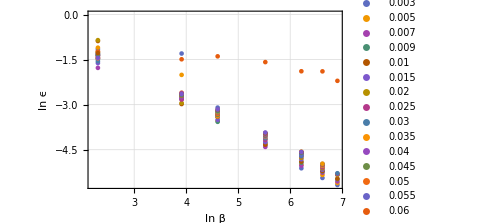
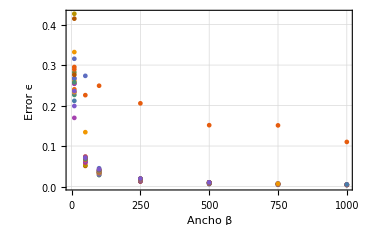
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[Log@errDataRptoCincoPptoCinco2D, PlotLegends->deltas, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"ln β", "ln ϵ"}],
	   ListPlot[errDataRptoCincoPptoCinco2D, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Ancho β", "Error ϵ"}]}
}]
```

#### Regresión lineal

```mathematica
lmRp5Pp5 = LinearModelFit[Flatten[Log[errDataRptoCincoPptoCinco2D],1], x, x]
```

FittedModel[0.631929-0.83749 x]

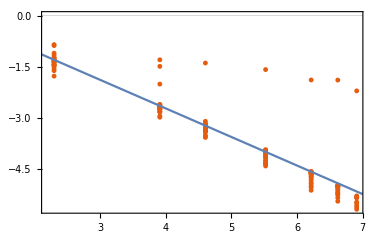
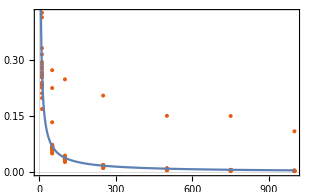
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 218.412 | 218.412 | 685.721 | 5.65473×10^-55
Error | 136 | 43.3179 | 0.318514 |  | 
Total | 137 | 261.73 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoCincoPptoCinco2D],1], PlotTheme->"Scientific"], Plot[lmRp5Pp5[x],{x,0,7}]], lmRp5Pp5["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoCincoPptoCinco2D,1], PlotTheme->"Scientific"], Plot[Exp[0.632]/x^(0.84), {x, 0,1000}, PlotRange->Full]]}
}]
```

### p = 0.8

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.5 y p = 0.8 que se hayan generado:*)
sampleNumsRptoCincoPptoOcho = Select[Flatten@getParamsPositions[0.5, 0.8], ((# < 1153) || (1188 < # < 1283)) && (# != 989)&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoCincoPptoOcho = Map[#[[1;;2]]&, allParams[[sampleNumsRptoCincoPptoOcho]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoCincoPptoOcho = Map[importAndGetMeanStd[#, 2, 0.8]&, sampleNumsRptoCincoPptoOcho];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoCincoPptoOcho4D = MapThread[Append[#1, #2]&, {βδValuesRptoCincoPptoOcho, errorsRptoCincoPptoOcho}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRptoCincoPptoOcho2D = Map[(#[[{1,3}]]&) /@ errDataRptoCincoPptoOcho4D[[Flatten[Position[errDataRptoCincoPptoOcho4D, {_, #, _}]]]]&, deltas];
errDataRptoCincoPptoOcho2D = Map[{#[[1]], Apply[Around,#[[2]]]}&, #]& /@ errDataRptoCincoPptoOcho2D;
```

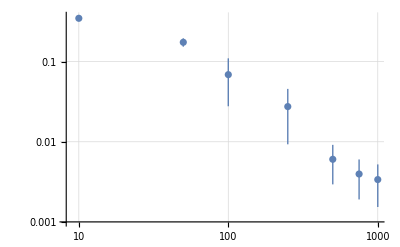
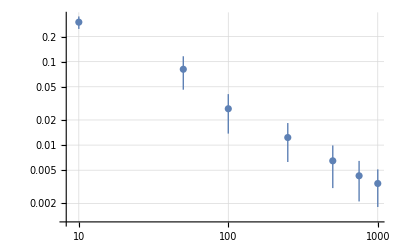
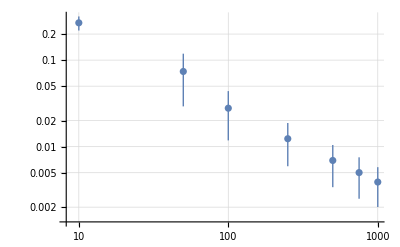
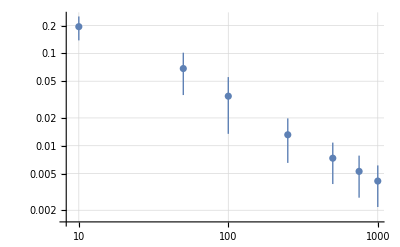
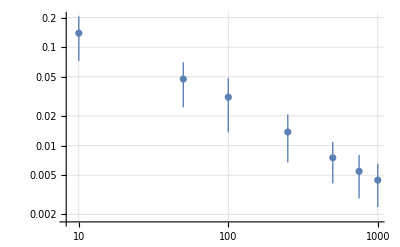
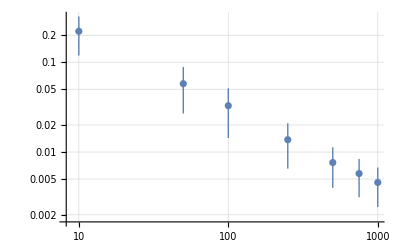
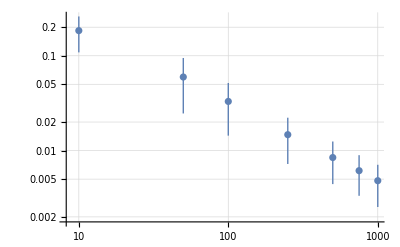
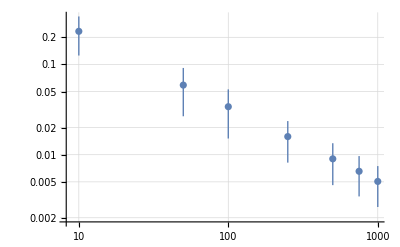

```mathematica
(*Graficamos una por una (por cada valor de δ):*)
Map[ListLogLogPlot[errDataRptoCincoPptoOcho2D[[#]], PlotLegends->deltas[[#]], GridLines->Automatic]&, Table[i, {i,22}]]
```

```mathematica
(*Todas juntas:*)
errDataRptoCincoPptoOcho2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoCincoPptoOcho2D;
```

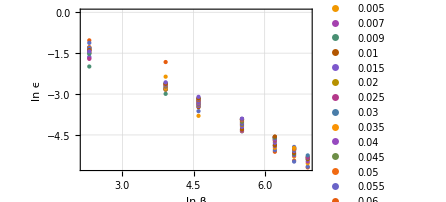
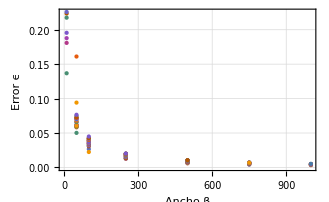
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[Log@errDataRptoCincoPptoOcho2D, PlotLegends->deltas, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"ln β", "ln ϵ"}],
	   ListPlot[errDataRptoCincoPptoOcho2D, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Ancho β", "Error ϵ"}]}
}]
```

#### Regresión lineal

```mathematica
lmRp5Pp8 = LinearModelFit[Flatten[Log[errDataRptoCincoPptoOcho2D],1], x, x]
```

FittedModel[0.628551-0.861902 x]

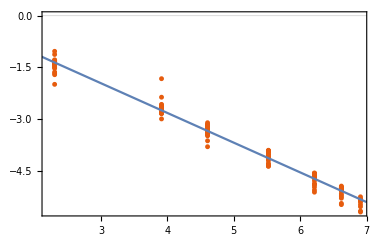
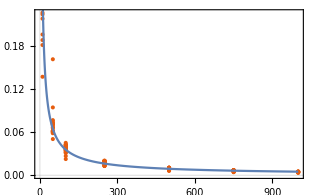
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 230.153 | 230.153 | 6511.99 | 4.08019×10^-116
Error | 135 | 4.77129 | 0.0353429 |  | 
Total | 136 | 234.924 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoCincoPptoOcho2D],1], PlotTheme->"Scientific"], Plot[lmRp5Pp8[x],{x,0,7}]], lmRp5Pp8["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoCincoPptoOcho2D,1], PlotTheme->"Scientific"], Plot[Exp[0.63]/x^(0.862), {x, 0,1000}, PlotRange->Full]]}
}]
```

## Jugando con las muestras obtenidas para r_z = 0.8

### p = 0.3

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.8 y p = 0.3 que se hayan generado:*)
sampleNumsRptoOchoPptoTres = Select[Flatten@getParamsPositions[0.8, 0.3], ((# < 1153) || (1188 < # < 1283))&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoOchoPptoTres = Map[#[[1;;2]]&, allParams[[sampleNumsRptoOchoPptoTres]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoOchoPptoTres = Map[importAndGetMeanStd[#, 3, 0.3]&, sampleNumsRptoOchoPptoTres];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoOchoPptoTres4D = MapThread[Append[#1, #2]&, {βδValuesRptoOchoPptoTres, errorsRptoOchoPptoTres}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRptoOchoPptoTres2D = Map[(#[[{1,3}]]&) /@ errDataRptoOchoPptoTres4D[[Flatten[Position[errDataRptoOchoPptoTres4D, {_, #, _}]]]]&, deltas];
errDataRptoOchoPptoTres2D = Map[{#[[1]], Apply[Around,#[[2]]]}&, #]& /@ errDataRptoOchoPptoTres2D;
```

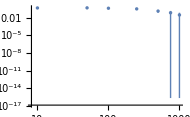
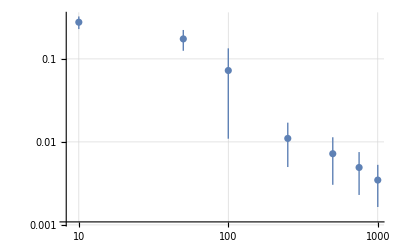
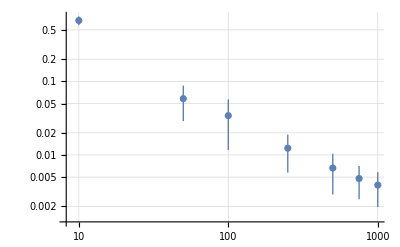
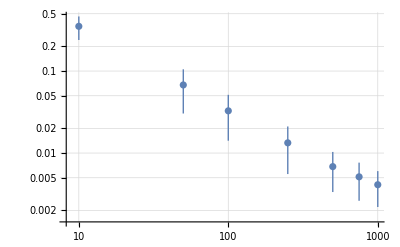
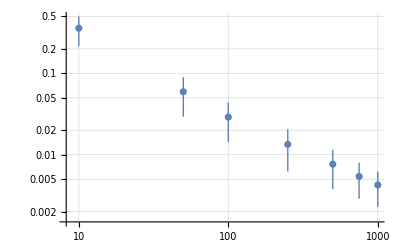
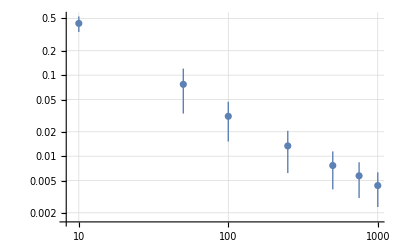
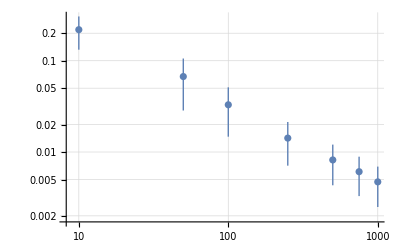
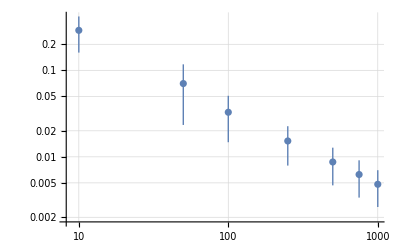
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Graficamos una por una (por cada valor de δ):*)
Map[ListLogLogPlot[errDataRptoOchoPptoTres2D[[#]], PlotLegends->deltas[[#]], GridLines->Automatic]&, Table[i, {i,22}]]
```

```mathematica
(*Todas juntas:*)
errDataRptoOchoPptoTres2D = Drop[Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoOchoPptoTres2D, 7]; (*Le retiramos los puntos raros*)
```

```mathematica
Grid[{{ListPlot[Log@errDataRptoOchoPptoTres2D, PlotLegends->deltas, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"ln β", "ln ϵ"}],
	   ListPlot[errDataRptoOchoPptoTres2D, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Ancho β", "Error ϵ"}]}
}]
```

-Graphics- | -Graphics-

#### Regresión lineal

```mathematica
lmRp8Pp3 = LinearModelFit[Flatten[Log[errDataRptoOchoPptoTres2D],1], x, x]
```

FittedModel[0.752816-0.868718 x]

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoOchoPptoTres2D],1], PlotTheme->"Scientific"], Plot[lmRp8Pp3[x],{x,0,7}]], lmRp8Pp3["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoOchoPptoTres2D,1], PlotTheme->"Scientific"], Plot[Exp[0.75]/x^(0.87), {x, 0,1000}, PlotRange->Full]]}
}]
```

-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 149.029 | 149.029 | 18609.7 | 3.37334×10^-104
Error | 88 | 0.704716 | 0.00800813 |  | 
Total | 89 | 149.733 |  |  |  | -Graphics-

### p = 0.5

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.8 y p = 0.5 que se hayan generado:*)
sampleNumsRptoOchoPptoCinco = Select[Flatten@getParamsPositions[0.8, 0.5], ((# < 1153) || (1188 < # < 1283))&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoOchoPptoCinco = Map[#[[1;;2]]&, allParams[[sampleNumsRptoOchoPptoCinco]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoOchoPptoCinco = Map[importAndGetMeanStd[#, 3, 0.5]&, sampleNumsRptoOchoPptoCinco];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoOchoPptoCinco4D = MapThread[Append[#1, #2]&, {βδValuesRptoOchoPptoCinco, errorsRptoOchoPptoCinco}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRptoOchoPptoCinco2D = Map[(#[[{1,3}]]&) /@ errDataRptoOchoPptoCinco4D[[Flatten[Position[errDataRptoOchoPptoCinco4D, {_, #, _}]]]]&, deltas];
errDataRptoOchoPptoCinco2D = Map[{#[[1]], Apply[Around,#[[2]]]}&, #]& /@ errDataRptoOchoPptoCinco2D;
```

```mathematica
(*Graficamos una por una (por cada valor de δ):*)
Map[ListLogLogPlot[errDataRptoOchoPptoCinco2D[[#]], PlotLegends->deltas[[#]], GridLines->Automatic]&, Table[i, {i,22}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Todas juntas:*)
errDataRptoOchoPptoCinco2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoOchoPptoCinco2D;
```

```mathematica
Grid[{{ListPlot[Log@errDataRptoOchoPptoCinco2D, PlotLegends->deltas, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"ln β", "ln ϵ"}],
	   ListPlot[errDataRptoOchoPptoCinco2D, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Ancho β", "Error ϵ"}]}
}]
```

-Graphics- | -Graphics-

#### Regresión lineal

```mathematica
lmRp8Pp5 = LinearModelFit[Flatten[Log[errDataRptoOchoPptoCinco2D],1], x, x]
```

FittedModel[0.886117-0.881311 x]

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoOchoPptoCinco2D],1], PlotTheme->"Scientific"], Plot[lmRp8Pp5[x],{x,0,7}]], lmRp8Pp5["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoOchoPptoCinco2D,1], PlotTheme->"Scientific"], Plot[Exp[0.87]/x^(0.88), {x, 0,1000}, PlotRange->Full]]}
}]
```

-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 241.866 | 241.866 | 724.704 | 2.40839×10^-56
Error | 136 | 45.3893 | 0.333745 |  | 
Total | 137 | 287.256 |  |  |  | -Graphics-

### p = 0.8

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.8 y p = 0.8 que se hayan generado:*)
sampleNumsRptoOchoPptoOcho = Select[Flatten@getParamsPositions[0.8, 0.8], ((# < 1153) || (1188 < # < 1283)) && (# != 990)&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoOchoPptoOcho = Map[#[[1;;2]]&, allParams[[sampleNumsRptoOchoPptoOcho]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoOchoPptoOcho = Map[importAndGetMeanStd[#, 3, 0.8]&, sampleNumsRptoOchoPptoOcho];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoOchoPptoOcho4D = MapThread[Append[#1, #2]&, {βδValuesRptoOchoPptoOcho, errorsRptoOchoPptoOcho}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRptoOchoPptoOcho2D = Map[(#[[{1,3}]]&) /@ errDataRptoOchoPptoOcho4D[[Flatten[Position[errDataRptoOchoPptoOcho4D, {_, #, _}]]]]&, deltas];
errDataRptoOchoPptoOcho2D = Map[{#[[1]], Apply[Around,#[[2]]]}&, #]& /@ errDataRptoOchoPptoOcho2D;
```

```mathematica
(*Graficamos una por una (por cada valor de δ):*)
Map[ListLogLogPlot[errDataRptoOchoPptoOcho2D[[#]], PlotLegends->deltas[[#]], GridLines->Automatic]&, Table[i, {i,22}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Todas juntas:*)
errDataRptoOchoPptoOcho2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoOchoPptoOcho2D;
```

```mathematica
Grid[{{ListPlot[Log@errDataRptoOchoPptoOcho2D, PlotLegends->deltas, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"ln β", "ln ϵ"}],
	   ListPlot[errDataRptoOchoPptoOcho2D, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Ancho β", "Error ϵ"}]}
}]
```

-Graphics- | -Graphics-

#### Regresión lineal

```mathematica
lmRp8Pp8 = LinearModelFit[Flatten[Log[errDataRptoOchoPptoOcho2D],1], x, x]
```

FittedModel[0.754739-0.876742 x]

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoOchoPptoOcho2D],1], PlotTheme->"Scientific"], Plot[lmRp8Pp8[x],{x,0,7}]], lmRp8Pp8["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoOchoPptoOcho2D,1], PlotTheme->"Scientific"], Plot[Exp[0.75]/x^(0.88), {x, 0,1000}, PlotRange->Full]]}
}]
```

-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 238.146 | 238.146 | 1622.18 | 4.22159×10^-77
Error | 135 | 19.8189 | 0.146806 |  | 
Total | 136 | 257.965 |  |  |  | -Graphics-

## Comentarios

Al observar estas primeras gráficas, se nota a primera vista que las muestras con δ = 0.001 se comportan distinto a todas las demás (de manera algo extraña). Esto sucede para casi todos los targets y swapPs. El comportamiento extraño consiste en que la desviación de cada error puede llegar a ser enorme, lo que significa que las distancias al target de dichas muestras se alejan mucho de la media. Además, al graficar los errores en función de β en escala Log-Log, no se observa la recta como sí se ve para los demás valores de δ. 

Veamos rápidamente la gráfica distancias de algunos de estos casos extraños.

```mathematica
(*Para rz = 0.5, p = 0.3.*)
testingSamples = Get["sampleMH_"<>ToString[#]<>".m"][[2]][[5001;;8000]]& /@ Flatten@Position[allParams, {_, 0.001, 0.3, targets[[2]]}];
```

```mathematica
sampleDists = distsToTarget[#, targets[[2]], 0.3]& /@ testingSamples;
```

```mathematica
sampleDistsMeans = Mean[#]& /@ sampleDists;
sampleDistsStdPlus = MapThread[(#1 + #2)&, {sampleDistsMeans, Map[StandardDeviation, sampleDists]}];
sampleDistsStdMinus = MapThread[(#1 - #2)&, {sampleDistsMeans, Map[StandardDeviation, sampleDists]}];
```

```mathematica
plots = MapThread[Show[ListPlot[#1], Plot[#2,{x,0,4000}, PlotStyle->Red], Plot[{#3, #4},{x,0,4000}, PlotStyle->Orange]]&, 
		  {sampleDists, sampleDistsMeans, sampleDistsStdPlus, sampleDistsStdMinus}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[ListPlot[sampleDists[[5]][[1000;;3000]], PlotTheme->"Detailed", FrameLabel->{Superscript[k,th]-"step", Style["d(C[ψ_k], ρ_t)",Italic]}, FrameStyle->Black], 
	 Plot[Mean[sampleDists[[5]][[1000;;3000]]],{x,0,2000}, PlotStyle->Red, PlotLegends->Style[ϵ, Black]]]
```

-Graphics-

```mathematica
Export["dists_plot.pdf",%91]
```

dists_plot.pdf

```mathematica
Directory[]
```

/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/gran_test_3

```mathematica
Length[sampleDists[[5]]]
```

3000

```mathematica
sampleDistsStdMinus (*tomando a partir de la muestra 3000*)
```

{0.285405,0.268588,0.182306,0.14792,-0.00387928,-0.00400041,-0.0209453}

```mathematica
sampleDistsStdMinus (*tomando a partir de la muestra 5000*)
```

{0.295818,0.251964,0.155025,0.126602,0.00340088,0.00220298,0.00160218}

Parece que el comportamiento extraño puede corregirse al tomar elementos de la muestra más cercanos al final, esto es, más “termalizados”. Si no nos deshacemos bien del burn-in no tendremos el error correcto.

## Graficando los resultados de las regresiones lineales

```mathematica
pendientes = {0.870149, 0.88187, 0.860747, 0.861268, 0.83749, 0.861902,0.868718, 0.881311, 0.876742};
ordenadas = {0.676218, 0.262353, 0.630121, 0.646099, 0.631929, 0.628551, 0.752816, 0.886117, 0.754739};
```

```mathematica
Show[ListPlot[pendientes, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"# Sample", "Slope"}], Plot[Mean[pendientes],{x,0,9}, PlotLegends->{"Mean"}]]
```

-Graphics-

```mathematica
Directory[]
```

/media/storage/ciencia/trabajo-con-carlos/tesis

```mathematica
Export["slopes_plot.png", %95]
```

slopes_plot.png

```mathematica
Show[ListPlot[ordenadas, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"# Sample", "Intercept"}], Plot[Mean[ordenadas],{x,0,9}, PlotLegends->{"Mean"}]]
```

-Graphics-

```mathematica
Export["intercepts_plot.png",%103]
```

intercepts_plot.png

```mathematica
{Mean[pendientes], Mean[ordenadas]}
```

{0.866689,0.652105}

```mathematica
{StandardDeviation[pendientes], StandardDeviation[ordenadas]}
```

{0.0137004,0.16934}